## Complex Mathematica Spikey

```mathematica
o=BoundaryDiscretizeRegion[PolyhedronData["Dodecahedron","BoundaryMeshRegion"],MaxCellMeasure->.001];
```

```mathematica
{inrad,outrad}={1/20 √(250+110 √5),1/4 (√3+√15)};
rescalef[r_]:=Re[1/2 (ArcSin[2 r-1]+π/2)];
coef1=0.01;
coef2=1.*^-5;
rescalef1[r_]:=coef1+(1-coef1)rescalef[(1-coef2)(r-inrad)/(outrad-inrad)+coef2/2];
```

```mathematica
ph=PolyhedronData["Dodecahedron","BoundaryMeshRegion"];
vertexasso=Association[Thread[Range@Length@#->#]&@MeshCoordinates@ph];
facecenterasso=Association[MapIndexed[#2[[1]]+Length@vertexasso->Mean[vertexasso/@#1]&,MeshCells[ph,{2}][[;;,1]]]];
ptsasso=Join[vertexasso,facecenterasso];
```

```mathematica
trianglecells=Flatten[MapIndexed[Function[{face,fid},Append[#,fid[[1]]+Length@vertexasso]&/@Partition[face,2,1,1]],MeshCells[ph,{2}][[;;,1]]],1];
```

Original parameters t1=0.05,t2=0.012,t3=0.035,t4=0.02,t5=0.05
Parameters for 3D printing t1=0.055,t2=0.04,t3=0.05,t4=0.1,t5=0.07

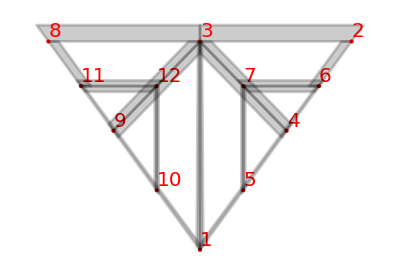

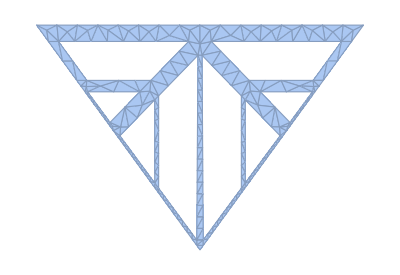

```mathematica
mesh=Block[{cr,rf,lf,prf,Trapezium,tra,l,ptsx,ptsy,ang,ptsl,poll,ratio=0.5,t1=0.05,t2=0.012,t3=0.035,t4=0.02,t5=0.05},
l=0.85065080835204;
ptsx=0.5;
ptsy=Sqrt[l^2-ptsx^2];
ang=ArcTan[ptsx/ptsy];

cr=#1[[1]] #2[[2]]-#2[[1]] #1[[2]]&;
rf=(#1*#3+#2*(1-#3))&;
lf=(#1+Normalize[#2-#1]*#3)&;
prf=rf[ptsl[[#1]],ptsl[[#2]],#3]&;
Trapezium[{a_List,b_List},{c_List,d_List},{t1_,t2_}]:=Polygon[{a,b,lf[b,d,t2/Abs@cr[Normalize[b-a],Normalize[b-d]]],lf[a,c,t1/Abs@cr[Normalize[b-a],Normalize[c-a]]]}];
Trapezium[{a_List,b_List},{c_List,d_List},t_]:=Trapezium[{a,b},{c,d},{t,t}];
Trapezium[{a_List,b_List},c_List,t_]:=Trapezium[{a,b},{c,c},t];
tra[{a_,b_},{c_,d_},t_]:=Trapezium[{ptsl[[a]],ptsl[[b]]},{ptsl[[c]],ptsl[[d]]},t];
tra[{a_,b_},c_,t_]:=tra[{a,b},{c,c},t];

ptsl=N@{{0,0},{ptsx,ptsy}*(ptsy-t1)/ptsy,{0,ptsy-t1},{ptsx,ptsy}*0.53};
ptsl=Join[ptsl,prf[4,#,ratio]&/@Range@3];
ptsl=DeleteDuplicates@Join[ptsl,{-#1,#2}&@@@ptsl];

poll={tra[{2,3},1,-t1],tra[{3,4},2,t1/2],tra[{3,4},1,t1/2],tra[{7,6},{3,2},t3/2],tra[{7,6},4,t3/2],tra[{2,6},{3,7},t5/2],tra[{6,1},{7,3},{t2/2,t4/2}],tra[{1,3},2,{t4/2,t2/2}],tra[{7,5},6,t2/2],tra[{7,5},{12,1},t2/2]};

poll=Join[poll,poll/.{a_Real,b_Real}:>{-a,b}];

Print@Graphics[{{Red,PointSize@Large,Point@ptsl,MapIndexed[Text[Style[#2[[1]],20],#1,{-1,-1}]&,ptsl]},{Opacity@.2,EdgeForm@Directive[Opacity@.4;AbsoluteThickness@2],poll}}];

DiscretizeRegion[RegionUnion@poll,MaxCellMeasure->0.0014]
]
```

```mathematica
tricells=Flatten[MeshPrimitives[mesh,{2}]/.{x_Real,y_Real}:>#3+(#2-#1)*x+(#1+#2-2#3)/2/Sqrt[0.85065080835204^2-0.5^2]*y&@@@Map[ptsasso,trianglecells,{2}],1];
(*Graphics3D[tricells]*)
```

This operation is very costy! Sometimes can be replaced by GatherBy[...,Round[#,1.*^-10]&] at some risk.

```mathematica
gresult=Gather[Flatten[tricells[[;;,1]],1],Norm[#1-#2]≤1.*^-6&];
ptasso=Association[Flatten[MapIndexed[#1->#2[[1]]&,gresult,{2}],1]];
newtricells=Polygon/@Map[ptasso,tricells[[;;,1]],{2}];
newtricoords=Mean/@gresult;
origmesh2d=MeshRegion[newtricoords,newtricells];
```

```mathematica
FindMeshDefects@origmesh2d
```

```mathematica
repairedmesh2d=RepairMesh[RepairMesh[origmesh2d,"TJunctionEdges"],"FlippedFaces"]
```

-Graphics3D-

Dump save this 2d mesh, just in case Mathematica crashes.

```mathematica
DumpSave[NotebookDirectory[]<>"2dmesh.mx",repairedmesh2d];
```

Reload if Mathematica crashes.

```mathematica
Get[NotebookDirectory[]<>"2dmesh.mx"]
```

```mathematica
convert2to3={Polygon[{#1,#2,#3}],Polygon[{#6,#5,#4}],Polygon[{#2,#1,#4,#5}],Polygon[{#1,#3,#6,#4}],Polygon[{#3,#2,#5,#6}]}&;
convertpoly[Polygon[{p1_,p2_,p3_,p4_}]]:={Polygon[{p1,p2,p3}],Polygon[{p1,p3,p4}]}
convertpoly[poly___]:={poly}
```

```mathematica
meshcoords=With[{mc=MeshCoordinates@repairedmesh2d},Riffle[mc,0.97mc]];
meshcells=Flatten[convertpoly/@Select[GatherBy[Flatten[convert2to3@@Flatten[{2#-1,2#},1]&/@MeshCells[repairedmesh2d,{2}][[;;,1]],1],Sort@*First],Length@#==1&][[;;,1]],1];
boundarymesh=BoundaryMeshRegion[meshcoords,meshcells]
```

-Graphics3D-

```mathematica
finalmesh=BoundaryMeshRegion[80rescalef1[Norm@#]Normalize@#&/@meshcoords,meshcells]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"Complex_Mathematica_Spikey_NOTFORPRINTING.stl",finalmesh];
```